```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
Msunt = ToString[Subscript["M","⊙"],FormatType->StandardForm];
```

```mathematica
hmf = ReadList[NotebookDirectory[]<>"hmf.dat",Table[Number,{3}]];
hmfi = Interpolation[hmf]
```

17
InterpolatingFunction[{{0.01, 20.}, {100000., 1. 10  }}, <>]

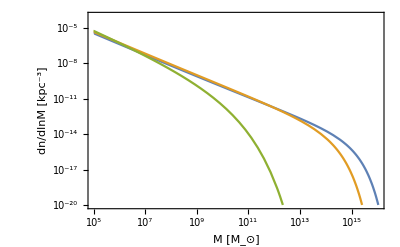

```mathematica
LogLogPlot[{hmfi[0.01,m],hmfi[1.,m],hmfi[10.,m]},{m,hmfi[[1,2,1]],hmfi[[1,2,2]]},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [kpc^-3]"},PlotRange->{All,{1.*^-20,1.*^-4}}]
```

```mathematica
N1 = ReadList[NotebookDirectory[]<>"N1.dat",Table[Number,{3}]];
N1[[-1,3]]
LLN1i = Interpolation[Log10@N1[[All,{1,2}]]]
LLN1cumi = Interpolation[{Log10@#[[1]],#[[3]]/N1[[-1,3]]}&/@N1[[1;;-2]]]
```

32.2191

InterpolatingFunction[…]

InterpolatingFunction[…]

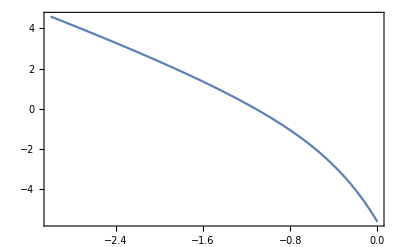

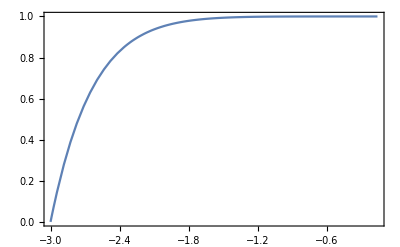

```mathematica
Plot[LLN1i[x],{x,LLN1i[[1,1,1]],LLN1i[[1,1,2]]}]
Plot[LLN1cumi[x],{x,LLN1cumi[[1,1,1]],LLN1cumi[[1,1,2]]},PlotRange->All]
```

```mathematica
P = ReadList[NotebookDirectory[]<>"lnmu.dat",Table[Number,{2}]];
zlist = DeleteDuplicates[P[[All,1]]]
P =GatherBy[P,First][[All,All,2]];
```

{0.2,1,2,3,4,5,6,7,8,9,10}

```mathematica
dx = 0.001;
Px = Table[{#[[1]],#[[2]]/(dx*Length[P[[j]]])}&/@Select[Sort@Tally[Round[Exp[P[[j]]-Mean[P[[j]]]],dx]],#[[2]]>9&],{j,Length@P}];
```

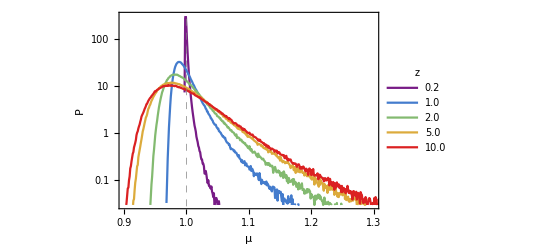

```mathematica
ListLogPlot[Px[[{1,2,3,6,11}]],Joined->True,PlotRange->{{0.9,1.3},{0.03,300}},GridLines->{{1},{}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"μ","P"},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),PlotLegends->Placed[LineLegend[Automatic,{"0.2","1.0","2.0","5.0","10.0"},LegendMarkerSize->{10,4},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendLabel->Style["z",14]],Scaled@{0.88,0.62}]]
```

```mathematica
dx = 0.001;
Plnx = Table[{#[[1]],#[[2]]/(dx*Length[P[[j]]])}&/@Sort@Tally[Round[P[[j]]-Mean[P[[j]]],dx]],{j,Length@P}];
```

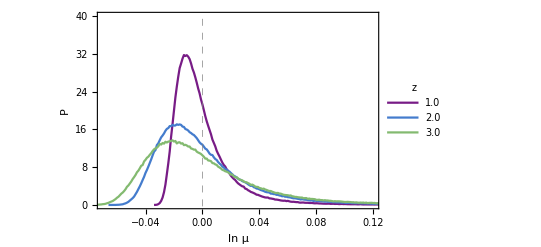

```mathematica
ListPlot[Plnx[[{2,3,4}]],Joined->True,PlotRange->{{-0.07,0.12},{0,40}},GridLines->{{0},{}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"ln μ","P"},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),PlotLegends->Placed[LineLegend[Automatic,{"1.0","2.0","3.0"},LegendMarkerSize->{10,4},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendLabel->Style["z",14]],Scaled@{0.88,0.62}]]
```

```mathematica
(*Put[Table[{zlist[[j]],Px[[j]]},{j,Length@zlist}],"Pmuz"];
Pmuz = Get["Pmuz"];
Pmuz[[All,1]]
ListLogPlot[Pmuz[[All,2]],Joined->True]*)
```